NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 2 : Find all the solutions of the equation z^3=8i and represent these geometrically.

(a) Solve the equation z^3 = 8i

```mathematica
sol=N[Solve[z^3==8I,z]]
```

{{z→0.-2. ⅈ},{z→1.73205+1. ⅈ},{z→-1.73205+1. ⅈ}}

```mathematica
z1=sol[[1,1,2]]
z2=sol[[2,1,2]]
z3=sol[[3,1,2]]
```

0.-2. ⅈ

1.73205+1. ⅈ

-1.73205+1. ⅈ

(b) Show that the roots lie on a circle with radius 2, centered at origin

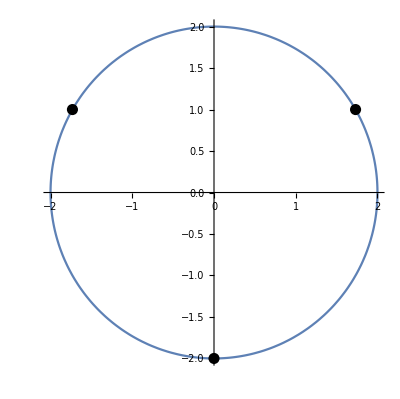

```mathematica
a=Graphics[{PointSize[0.02],
Point[{Re[z1],Im[z1]}],
Point[{Re[z2],Im[z2]}],
Point[{Re[z3],Im[z3]}]
}];
b=PolarPlot[2,{τ,0,2π}];
Show[b,a]
```